### Basic:

```mathematica
FNJ=FileNameJoin;
```

```mathematica
RelativeDir[dir_]:=FileNameJoin[{NotebookDirectory[],dir}]
```

```mathematica
Replicate[list_,n_]:=Flatten[Transpose[ConstantArray[list,n]]]
```

```mathematica
ToText[list_]:=StringJoin[Riffle[ToString[#]&/@list,"\n"]]
```

```mathematica
ShiftLeft[list_,n_]:=Drop[PadLeft[list,Length[list]+n],-n]
```

```mathematica
ShiftRight[list_,n_]:=Drop[PadRight[list,Length[list]+n],n]
```

```mathematica
Half[list_]:= Take[list, Floor[Length[list]/2]]
```

### Before simulation:

```mathematica
(*-------parameters-------*)
td = 3; blocks = 4; l = 100;
(*------------------------*)
data=RandomInteger[{-16,16},l];
ker = RandomInteger[{-16,16},td*blocks];
upKer = RandomInteger[{-16,16},td*6];
```

```mathematica
expected=ListConvolve[Reverse[ker],data,1,0];
```

```mathematica
Max[Abs[expected]]
```

752

```mathematica
(*Export[RelativeDir["data.dat"],ToText[Replicate[data,td]]];Export[RelativeDir["coefs.dat"],ToText[ker]];Export[RelativeDir["upsamp_coefs.dat"],ToText[upKer]];*)
```

### After simulation:

```mathematica
ker
```

{6,5,2,3,-1,15,0,12,8,-3,-16,-10}

```mathematica
expected
```

{-100,-230,-152,53,179,-31,-145,-294,-234,157,499,752,611,307,46,-268,-112,34,154,127,-627,-180,-360,76,-53,390,84,354,-385,-99,13,65,298,77,240,-257,-298,-368,67,-21,54,-214,82,-162,73,530,231,-168,-377,158,167,359,382,261,143,-105,147,113,196,-106,562,41,-113,-74,-290,-52,-66,613,-227,-81,-377,149,-67,-627,-128,-349,-371,-397,37,-13,-37,133,-101,183,713,325,196,202,390,-5,-57,125,-155,-444,-452,187,195,321,78,-225}

```mathematica
upKer
```

{-7,3,14,3,11,-5,16,2,2,3,5,-11,2,6,16,-1,13,-14}

```mathematica
Max[lol]
```

lol

```mathematica
upIn=Flatten@Riffle[expected,{ConstantArray[0,2]}]
```

{-100,0,0,-230,0,0,-152,0,0,53,0,0,179,0,0,-31,0,0,-145,0,0,-294,0,0,-234,0,0,157,0,0,499,0,0,752,0,0,611,0,0,307,0,0,46,0,0,-268,0,0,-112,0,0,34,0,0,154,0,0,127,0,0,-627,0,0,-180,0,0,-360,0,0,76,0,0,-53,0,0,390,0,0,84,0,0,354,0,0,-385,0,0,-99,0,0,13,0,0,65,0,0,298,0,0,77,0,0,240,0,0,-257,0,0,-298,0,0,-368,0,0,67,0,0,-21,0,0,54,0,0,-214,0,0,82,0,0,-162,0,0,73,0,0,530,0,0,231,0,0,-168,0,0,-377,0,0,158,0,0,167,0,0,359,0,0,382,0,0,261,0,0,143,0,0,-105,0,0,147,0,0,113,0,0,196,0,0,-106,0,0,562,0,0,41,0,0,-113,0,0,-74,0,0,-290,0,0,-52,0,0,-66,0,0,613,0,0,-227,0,0,-81,0,0,-377,0,0,149,0,0,-67,0,0,-627,0,0,-128,0,0,-349,0,0,-371,0,0,-397,0,0,37,0,0,-13,0,0,-37,0,0,133,0,0,-101,0,0,183,0,0,713,0,0,325,0,0,196,0,0,202,0,0,390,0,0,-5,0,0,-57,0,0,125,0,0,-155,0,0,-444,0,0,-452,0,0,187,0,0,195,0,0,321,0,0,78,0,0,-225}

```mathematica
lol=ListConvolve[Reverse[upKer],upIn,1,0]
```

{1400,-1300,100,1620,-3590,30,-452,-3856,-608,-844,-1573,-2647,54,325,-4509,2161,-2198,-1874,-2789,-3432,2622,102,-4362,3998,-48,-3465,-1119,-337,-927,-5173,-2197,3983,-5809,-5299,9418,-2894,-4643,11808,6258,-5857,13440,13264,-1246,12959,14831,5559,9318,9820,4861,6757,1195,7791,3732,-3682,3152,2537,-6721,2072,-289,-2635,5992,-8587,3427,-10339,-5121,2657,9017,-6845,375,-4577,-1467,-12065,10471,-8909,-6525,-15742,551,-2179,5079,-1181,1933,-13428,6706,2884,12239,-2036,6894,-11192,2472,3276,8217,452,1820,-977,3804,-6022,3408,958,-5346,-1894,896,3320,-6727,5048,2580,7044,-166,5840,-3006,-589,2175,7478,-5636,986,-4184,-470,-5628,9463,-4414,-8168,-4673,-3874,-4878,1893,-7371,2313,-10695,-357,2093,7085,-2606,16,-5508,490,-3266,-2480,4490,-578,713,6484,200,2322,462,2328,-1524,-3377,10567,-7562,5463,3359,10266,5029,-6687,-772,4550,-7704,-1592,3620,3410,-7225,8421,7365,67,8364,6664,2194,6012,7194,-1673,7797,2881,6254,6129,263,176,6107,-2607,6198,-69,1873,-13699,9178,2798,11469,5451,3211,-3554,3870,-18,3175,-889,7273,-93,1167,2887,4339,-875,-6369,4273,-3888,-2718,-10858,5580,-4972,14022,-3119,71,-13173,-924,2284,7307,-6178,9508,-11670,5361,-2477,17024,-2682,-7034,2540,-10134,-3746,-6454,-9853,493,3578,-8066,226,2185,-9101,-11987,5402,-16486,-4852,-11625,-7743,-3523,4352,-6897,-7191,-3922,-6296,-4900,-5446,-3964,1752,-1820,-1510,2938,-5132,2332,-876,-5674,9682,1458,3460,10568,692,-2654,7717,4287,-4170,8563,13829,-4737,16304,6660,12837,9391,511,402,4714,2762,-93,4848,5220,5665,3336,-90,7732,-5076,-3148,1394,-9707,963,-6699,-1607,-4129,6871,-821,-9621,-4285,25,-6849,-1683,-2015,5893,-6006}

```mathematica
2^13
```

8192

```mathematica
Floor[lol/2^8]
```

{5,-6,0,6,-15,0,-2,-16,-3,-4,-7,-11,0,1,-18,8,-9,-8,-11,-14,10,0,-18,15,-1,-14,-5,-2,-4,-21,-9,15,-23,-21,36,-12,-19,46,24,-23,52,51,-5,50,57,21,36,38,18,26,4,30,14,-15,12,9,-27,8,-2,-11,23,-34,13,-41,-21,10,35,-27,1,-18,-6,-48,40,-35,-26,-62,2,-9,19,-5,7,-53,26,11,47,-8,26,-44,9,12,32,1,7,-4,14,-24,13,3,-21,-8,3,12,-27,19,10,27,-1,22,-12,-3,8,29,-23,3,-17,-2,-22,36,-18,-32,-19,-16,-20,7,-29,9,-42,-2,8,27,-11,0,-22,1,-13,-10,17,-3,2,25,0,9,1,9,-6,-14,41,-30,21,13,40,19,-27,-4,17,-31,-7,14,13,-29,32,28,0,32,26,8,23,28,-7,30,11,24,23,1,0,23,-11,24,-1,7,-54,35,10,44,21,12,-14,15,-1,12,-4,28,-1,4,11,16,-4,-25,16,-16,-11,-43,21,-20,54,-13,0,-52,-4,8,28,-25,37,-46,20,-10,66,-11,-28,9,-40,-15,-26,-39,1,13,-32,0,8,-36,-47,21,-65,-19,-46,-31,-14,17,-27,-29,-16,-25,-20,-22,-16,6,-8,-6,11,-21,9,-4,-23,37,5,13,41,2,-11,30,16,-17,33,54,-19,63,26,50,36,1,1,18,10,-1,18,20,22,13,-1,30,-20,-13,5,-38,3,-27,-7,-17,26,-4,-38,-17,0,-27,-7,-8,23,-24}

```mathematica
result
```

result

```mathematica
result=Flatten[Import[RelativeDir[FNJ[{"edit_firIP_v1_0.sim","sim_1","behav","xsim","out.dat"}]]]];
```

```mathematica
LongestCommonSubsequence[result,lol]
```

{}

### Random:

```mathematica
2224189. /2^16
```

33.9384

### Samples from fpga:

```mathematica
fker = Flatten@Import[RelativeDir["coefs.dat"]]
```

{4563,-5780,100032,-103434,12,-15,250,43032,15003,-79934,25666,76498}

```mathematica
fupker =  Flatten@Import[RelativeDir["upsamp_coefs.dat"]]
```

{-10009,10343,15133,11501,-111,5}

```mathematica
datain=Downsample[Flatten@Import[RelativeDir["data.dat"]],3]
```

{10,8,8,-15,-14,7,8,9,8,15,10,-3,-12,12,-16,13,1,-4,2,-15,2,-14,3,-6,-3,-14,8,11,-3,3,1,0,-7,-4,-9,-16,14,13,-2,-10,-12,1,-1,14,14,-2,7,-2,-10,-12,2,-9,9,4,2,7,-16,2,-9,-8,2,16,16,6,-3,0,0,8,-15,9,3,-15,-14,7,5,5,10,-3,10,-14,-2,13,7,-14,-5,-6,9,-8,-1,5,-1,12,15,16,9,-3,-4,14,6,-8}

```mathematica
Floor[ListConvolve[Reverse[fker],datain,1,0]/2^12]
```

{186,212,4,-350,-378,449,496,-127,-326,298,221,412,-314,-87,77,-224,344,-443,-15,257,133,-572,605,-720,144,-210,-7,889,-651,130,-218,299,-261,208,-593,-369,566,411,-318,-554,124,199,304,268,-491,-191,216,444,-120,-549,278,-372,-86,558,-356,243,6,-81,-129,52,-461,588,260,-301,325,-358,556,163,-493,-437,409,-190,-321,376,398,-427,572,-605,218,371,-233,15,352,-655,-422,610,-84,472,-629,-134,224,537,171,264,-373,293,-242,367,502,-767}

```mathematica
Floor[764980/2^12]
```

46

```mathematica
Floor[ListConvolve[Reverse[fupker], Flatten[Riffle[Floor[ListConvolve[Reverse[fker],datain]/2^12],{{0,0}}]]]/2^20]
```

{-8,-5,-4,2,-2,-1,1,1,0,-4,-4,-3,5,4,3,-9,-7,-5,4,-1,-1,2,3,2,-1,1,1,-8,-9,-6,12,8,6,-14,-11,-8,8,2,1,-4,-4,-3,1,-1,-1,9,12,8,-16,-10,-7,7,1,1,-4,-4,-3,5,4,2,-6,-4,-3,4,2,2,-9,-9,-6,1,-6,-4,9,8,5,-1,5,4,-8,-5,-4,-4,-8,-6,6,1,1,0,2,1,1,4,2,0,3,2,-8,-8,-5,2,-3,-2,4,3,2,2,6,4,-6,-2,-2,-5,-8,-6,8,4,2,-7,-6,-4,2,-2,-1,6,8,5,-10,-6,-4,6,3,2,-3,0,0,-1,-2,-1,-1,-2,-2,1,0,0,-6,-7,-5,10,8,5,-3,3,2,-6,-5,-4,6,4,3,-8,-6,-4,9,8,5,-4,2,1,-7,-8,-5,-1,-7,-5,8,5,4,-6,-3,-2,-2,-5,-4,7,5,3,0,5,3,-9,-7,-5,10,8,5,-13,-9,-6,8,3,2,1,5,3,-7,-4,-3,2,0,0,3,5,3,-11,-10,-7,1,-7,-5,10,8,6,-7,-2,-1,5,6,4,-12,-10,-7,4,-2,-2,3,3,2,3,7,5,-4,2,1,1,3,2,-7,-6,-4,6,4,2,-6,-4,-3,6,5,3,2,7}

```mathematica
2^14
```

16384

```mathematica
85*6229+960
```

530425

```mathematica
snaps=Reverse/@Import[RelativeDir["snap20.dat"]];
```

```mathematica
(*afirIn = snaps[[2]]*)
```

```mathematica
(*afirOut = snaps[[10]]*)
```

```mathematica
(*expafirOut=Floor[ListConvolve[fupker, Flatten[Riffle[Downsample[afirIn,3],{{0,0}}]]]/2^20]*)
```

```mathematica
(*LongestCommonSubsequence[afirOut,expafirOut]*)
```

```mathematica
snaps[[2]]
```

{-4350,-4118,-4022,-4308,-4300,-3796,-4202,-4350,-3486,-4022,-4308,-3121,-3796,-4202,-2666,-3486,-4022,-2165,-3121,-3796,-1690,-2666,-3486,-1190,-2165,-3121,-649,-1690,-2666,-124,-1190,-2165,417,-649,-1690,940,-124,-1190,1410,417,-649,1895,940,-124,2395,1410,417,2863,1895,940,3245,2395,1410,3559,2863,1895,3816,3245,2395,4021,3559,2863,4141,3816,3245,4177,4021,3559,4204,4141,3816,4100,4177,4021,3865,4204,4141,3490,4100,4177,2976,3865,4204,2295,3490,4100,1562,2976,3865,832,2295,3490,47,1562,2976,-739,832,2295,-1456,47}

```mathematica
firIn=Downsample[snaps[[2]],3,1]; firOut = Downsample[snaps[[3]],3,1]
```

{52252,45290,36679,26759,15945,4652,-6764,-17992,-28719,-38586,-47210,-54232,-59412,-62685,-64165,-64068,-62623,-60010,-56340,-51680,-46117,-39777,-32819,-25412,-17708,-9833,-1895,6014,13816,21444,28815,35808,42261,48004}

```mathematica
firOutExp=Floor[ListConvolve[fker,firIn]/2^12]
```

{-39777,-32819,-25412,-17708,-9833,-1895,6014,13816,21444,28815,35808,42261,48004,52889,56826,59762,61648,62384,61796,59665}

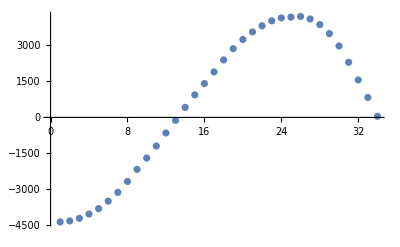

```mathematica
ListPlot[firIn]
```

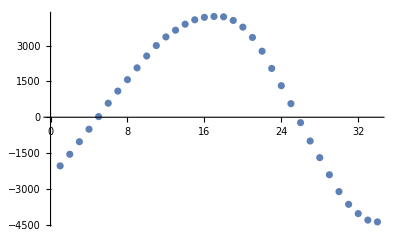

-Graphics-

```mathematica
firOut
```

{52252,45290,36679,26759,15945,4652,-6764,-17992,-28719,-38586,-47210,-54232,-59412,-62685,-64165,-64068,-62623,-60010,-56340,-51680,-46117,-39777,-32819,-25412,-17708,-9833,-1895,6014,13816,21444,28815,35808,42261,48004}

```mathematica
LongestCommonSubsequence[firOutExp,firOut]
```

{-39777,-32819,-25412,-17708,-9833,-1895,6014,13816,21444,28815,35808,42261,48004}

```mathematica
s
```

s

```mathematica
TableForm[Join[{Range[Length[snaps]]},Transpose@snaps]];
```

```mathematica
rng=Range[#,#+3]&/@Range[1,5*3,3];
```

```mathematica
(*(Drop[ShiftRight[snaps[[#1]],1]+(snaps[[#2]]*snaps[[#3]]),-4]==Drop[snaps[[#4]],4])&@@@rng*)
```

### Upsampling:

```mathematica
upker={0.004349354184333842,-0.012460526975242473,-0.04179305187785534,0.11580155515788863,0.4377645703903624,0.4377645703903624,0.11580155515788867,-0.04179305187785537,-0.012460526975242473,0.004349354184333842};
```

```mathematica
f=0.113;
```

```mathematica
in=Sin[2*π*f*#]&/@Range[100];
```

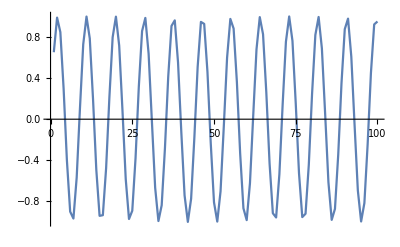

```mathematica
ListPlot[in,Joined->True]
```

```mathematica
inR=Append[Flatten@Riffle[in,0],0]
```

{0.651834,0,0.988652,0,0.847678,0,0.297042,0,-0.397148,0,-0.899405,0,-0.967001,0,-0.567269,0,0.106611,0,0.728969,0,0.999033,0,0.786288,0,0.193549,0,-0.492727,0,-0.940881,0,-0.934329,0,-0.476238,0,0.212007,0,0.797794,0,0.998027,0,0.715936,0,0.0878512,0,-0.58269,0,-0.971632,0,-0.891007,0,-0.379779,0,0.314987,0,0.857527,0,0.985645,0,0.637424,0,-0.0188484,0,-0.666012,0,-0.991308,0,-0.837528,0,-0.278991,0,0.414376,0,0.907484,0,0.962028,0,0.551646,0,-0.125333,0,-0.741742,0,-0.999684,0,-0.774503,0,-0.175023,0,0.509041,0,0.947098,0,0.927445,0,0.45958,0,-0.230389,0,-0.809017,0,-0.996666,0,-0.70265,0,-0.06906,0,0.597905,0,0.975917,0,0.882291,0,0.362275,0,-0.33282,0,-0.867071,0,-0.982287,0,-0.622788,0,0.0376902,0,0.679953,0,0.993611,0,0.827081,0,0.260842,0,-0.431456,0,-0.915241,0,-0.956712,0,-0.535827,0,0.144011,0,0.754251,0,0.99998,0,0.762443,0,0.156434,0,-0.525175,0,-0.952979,0,-0.920232,0,-0.442758,0,0.24869,0,0.819952,0,0.994951,0,0.689114,0,0.0502443,0,-0.612907,0,-0.979855,0,-0.873262,0,-0.344643,0,0.350534,0,0.876307,0,0.978581,0,0.60793,0,-0.0565185,0,-0.693653,0,-0.995562,0,-0.816339,0,-0.242599,0,0.448383,0,0.922673,0,0.951057,0}

```mathematica
out=ListConvolve[fupker/2^16,inR,1,0];
```

```mathematica
LinInt[list_]:=Module[{i,intlist={}},For[i=1,i< Length[list],i++,AppendTo[intlist,list[[i]]];AppendTo[intlist,(list[[i]]+list[[i+1]])/2]];AppendTo[intlist,Last[list]];AppendTo[intlist,2*Last[intlist]-intlist[[-2]]];intlist]
```

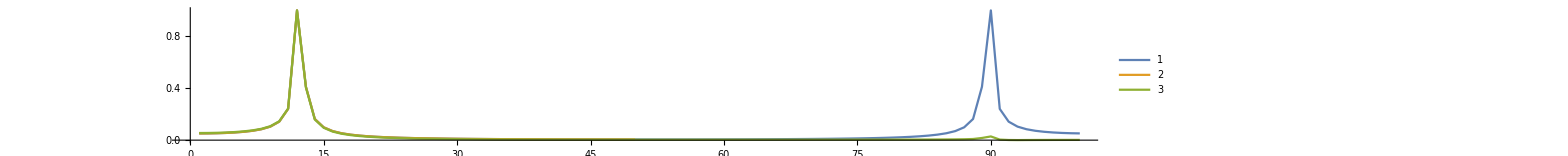

```mathematica
ListPlot[{Half@Abs@Fourier@inR/Max[Half@Abs@Fourier@inR],(Half@Abs@Fourier@in)/Max[Half@Abs@Fourier@in],(Half@Abs@Fourier@LinInt@in)/Max[Half@Abs@Fourier@LinInt@in]},Joined->True,PlotRange->All,ImageSize->5000, PlotLegends->Automatic,AspectRatio->0.1]
```

```mathematica
Manipulate[ListPlot[Abs@Fourier@Flatten@Riffle[Sin[2*π*f*#]&/@Range[100],{{0,0}}],Joined->True,ImageSize->300,PlotRange->{0,3}],{f,0,0.5,0.01}]
```

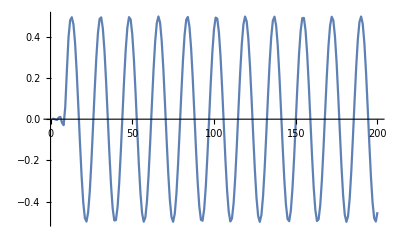

```mathematica
ListPlot[out,Joined->True]
```